```mathematica
exp(-(((log(wvecright[1:Lr])-log(w)-log(beta))^2)/(2*sigmaval*sigmaval))
```

```mathematica
Integrate[
```

```mathematica
mort_eter<-function(w){return(sum(((1-fbar)*exp(-(((log(wvecright[1:Lr])-log(w)-log(beta))^2)/(2*sigmaval*sigmaval)))*gamma*kappaRval*wvecright[1:Lr]^(qval-lambda))*(wvecright[2:(Lr+1)]-wvecright[1:Lr])))}
```

```mathematica
((1-fbar)*exp(-(((log(wvecright[1:Lr])-log(w)-log(beta))^2)/(2*sigmaval*sigmaval)))*gamma*kappaRval*wvecright[1:Lr]^(qval-lambda))
```

```mathematica
Integrate[(1-fbar)*Exp[-((y-Log[w]-Log[beta])^2)/(2*sigma*sigma)]*kappa*gamma*Exp[y*(1+q-lambda)],{y,Log[W],Infinity}]
```

ConditionalExpression[-(beta^(1-lambda+q) ⅇ^(1/2 (1-lambda+q)^2 sigma^2) (-1+fbar) gamma kappa √(π/2) w^(1-lambda+q) (√(1/sigma^2) Erf[1/(√2)(√((sigma^2-lambda sigma^2+q sigma^2+Log[beta]+Log[w]-Log[W])^2/sigma^2))] (sigma^2-lambda sigma^2+q sigma^2+Log[beta]+Log[w]-Log[W])+√(1/sigma^2(sigma^2-lambda sigma^2+q sigma^2+Log[beta]+Log[w]-Log[W])^2)))/(√(1/sigma^2) √(1/sigma^2(sigma^2-lambda sigma^2+q sigma^2+Log[beta]+Log[w]-Log[W])^2)),Re[sigma^2]>0]

```mathematica
((1-fbar)*exp(-(((log(wvecright[1:Lr])-log(w)-log(beta))^2)/(2*sigmaval*sigmaval)))*gamma*kappaRval*wvecright[1:Lr]^(qval-lambda))
```

```mathematica
(1-fbar)*gamma*kappaRval*Exp[-((y-Log[w]-Log[beta])^2)/(2*sigma*sigma)]*Exp[(q+1-lambda)*y]
```

```mathematica
Integrate[Exp[-((y-A)^2)/B]*Exp[c*y],y]
```

-1/2 √B ⅇ^(A c+(B c^2)/4) √π Erf[(B c+2 (A-y))/(2 √B)]

```mathematica
Ex=-1/2 √B ⅇ^(A c+(B c^2)/4) √π Erf[(B c+2 (A-y))/(2 √B)]
```

-1/2 √B ⅇ^(A c+(B c^2)/4) √π Erf[(B c+2 (A-y))/(2 √B)]

```mathematica
Ex/.A->Infinity
```

-1/2 √B ⅇ^((B c^2)/4+c ∞) √π Erf[∞/(√Sign[B])]

```mathematica
0
```

```mathematica
(* if q+1-lambda<- *)
```

```mathematica
(* so integral is -indef int al lower lim *)
```

```mathematica
kappa=0.4;
q=0.8;
n=2/3;
beta=100;
sigma=1.3;
gamma=600.4424;
fbar=0.5;
k=0;
we=0.001;
eta=1/4;
u=10;
matsize=19.35659;
alpha=0.17
```

0.17

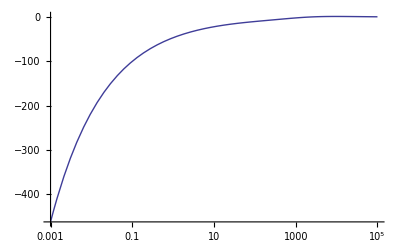

```mathematica
LogLinearPlot[((1-fbar)*gamma*kappa*(-1)*(-1/2 √B ⅇ^(A c+(B c^2)/4) √π Erf[(B c+2 (A-y))/(2 √B)])/.{A->Log[w]+Log[beta],B->(2*sigma*sigma),c->(q+1-lambda),y->Log[W]})/.{lambda->2+q-n,W->10^5},{w,0.001,10^5}]
```

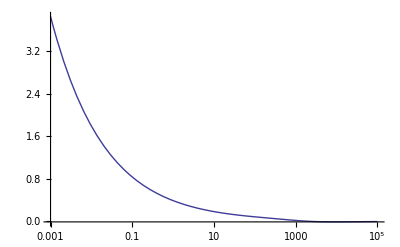

```mathematica
LogLinearPlot[((-1/2 √B ⅇ^(A c+(B c^2)/4) √π Erf[(B c+2 (A-y))/(2 √B)])/.{A->Log[w]+Log[beta],B->(2*sigma*sigma),c->(q+1-lambda),y->Log[W]})/.{lambda->2+q-n,W->10^5},{w,0.001,10^5}]
```

```mathematica
W=10^5
lambda=2+q-n
```

100000

2.13333

```mathematica
etmort[w_]:=NIntegrate[(1-fbar)*Exp[-((y-Log[w]-Log[beta])^2)/(2*sigma*sigma)]*kappa*gamma*Exp[y*(1+q-lambda)],{y,Log[W],Infinity}]
```

NIntegrate::inumr: The integrand 120.088\ ⅇ^-0.333333\ y - 0.295858\ (y - Log[« 1 »] - Log[« 1 »])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 11.5129}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

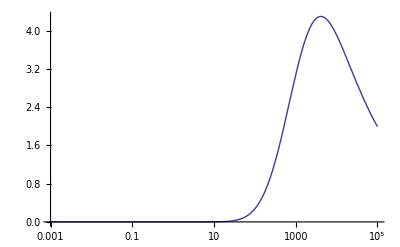

```mathematica
LogLinearPlot[etmort[w],{w,0.001,10^5}]
```

```mathematica
etmorttry[w_]:=NIntegrate[(1-fbar)*Exp[-((y-Log[w]-Log[beta])^2)/(2*sigma*sigma)]*kappa*gamma*Exp[y*(1+q-lambda)],{y,Log[W],Infinity}]
```

```mathematica
LogLinearPlot[etmorttry[w],{w,0.001,10^5}]
```

NIntegrate::inumr: The integrand 120.088\ ⅇ^-0.333333\ y - 0.295858\ (y - Log[« 1 »] - Log[« 1 »])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 11.5129}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

-Graphics-

```mathematica
Re[sigma^2]>0
```

```mathematica
aw=Integrate[(1-fbar)*Exp[-((y-Log[w]-Log[beta])^2)/(2*sigma*sigma)]*kappa*gamma*Exp[y*(1+q-lambda)],{y,Log[W],Infinity}]
```

ConditionalExpression[-beta^(1-lambda+q) ⅇ^(1/2 (1-lambda+q)^2 sigma^2) (-1+fbar) gamma kappa √(π/2) sigma w^(1-lambda+q) (√(1/sigma^2) sigma+Erf[((1-lambda+q) sigma^2+Log[beta]+Log[w]-Log[W])/(√2 sigma)]),Re[sigma^2]>0]

```mathematica
(-beta^(1 - lambda + q))*E^((1/2)*(1 - lambda + q)^2*sigma^2)*(-1 + fbar)*gamma*kappa*Sqrt[Pi/2]*sigma*w^(1 - lambda + q)*
  (Sqrt[1/sigma^2]*sigma + Erf[((1 - lambda + q)*sigma^2 + Log[beta] + Log[w] - Log[W])/(Sqrt[2]*sigma)])
```

```mathematica
etmortgood[w_]:=(-beta^(1 - lambda + q))*E^((1/2)*(1 - lambda + q)^2*sigma^2)*(-1 + fbar)*gamma*kappa*Sqrt[Pi/2]*sigma*w^(1 - lambda + q)*
  (Sqrt[1/sigma^2]*sigma + Erf[((1 - lambda + q)*sigma^2 + Log[beta] + Log[w] - Log[W])/(Sqrt[2]*sigma)])
```

```mathematica
kappa=0.4;
q=0.8;
n=2/3;
beta=100;
sigma=1.3;
gamma=600.4424;
fbar=0.5;
k=0;
we=0.001;
eta=1/4;
u=10;
matsize=19.35659;
alpha=0.17
W=10^5
lambda=2+q-n
```

0.17

100000

2.13333

```mathematica
LogLinearPlot[etmortgood[w],{w,0.001,10^5}]
```

-Graphics-